```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fontsize=28;
```

## Best result up to now

### Short time window

```mathematica
data=Import["2021-02-10\\1.Wfm.csv","Table","FieldSeparators"->{";"}];
t=Subdivide[-1.5*^-007,8.5*^-007,5000-1];
```

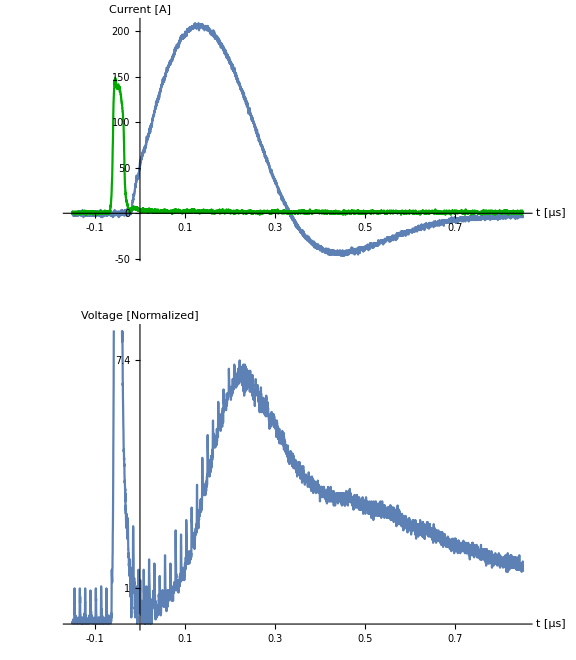

```mathematica
GraphicsColumn[{
ListLinePlot[{Thread[{t,data[[All,2]]}],Style[Thread[{t,3data[[All,1]]}],Darker[Green]]},PlotRange->All
,
Ticks->{Table[{i*10^-7,0.1i,0.04,Thick},{i,-1,9,2}], Table[{i,10i,0.04,Thick},{i,-5,20,5}]}
,
TicksStyle->Directive[fontsize,Black]
,
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Current [A]",fontsize,Black]}
,AspectRatio->#]
,
ListLinePlot[{Thread[{t,data[[All,3]]}]},PlotRange->{0,0.028}
,Ticks->{Table[{i*10^-7,0.1i,0.04,Thick},{i,-1,9,2}], {{Max[data[[All,3]]⟦;;200⟧],"1 ",0.04,Thick},{Max[data⟦All,3⟧⟦900;;⟧],NumberForm[Max[data[[All,3]]⟦900;;⟧]/Max[data[[All,3]]⟦;;200⟧],2],0.04,Thick}}}
,
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Voltage\n[Normalized]",fontsize,Black]}
,AspectRatio->#]
}
,ImageSize->Large]&[0.5]
```

### Long time window

```mathematica
data=data=Import["2021-02-10\\2.Wfm.csv","Table","FieldSeparators"->{";"}];
t=Subdivide[-6*^-007,3.4*^-006,10000-1];
```

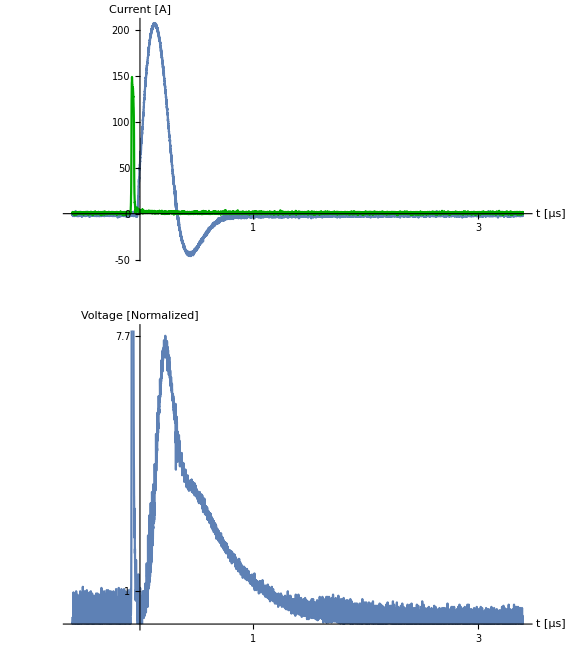

```mathematica
GraphicsColumn[{
ListLinePlot[{Thread[{t,data[[All,2]]}],Style[Thread[{t,3data[[All,1]]}],Darker[Green]]},PlotRange->All
,
Ticks->{Table[{i*10^-6,i,0.04,Thick},{i,-1,9,1}], Table[{i,10i,0.04,Thick},{i,-5,20,5}]}
,
TicksStyle->Directive[fontsize,Black]
,
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Current [A]",fontsize,Black]}
,AspectRatio->#]
,
ListLinePlot[{Thread[{t,data[[All,3]]}]},PlotRange->{0,0.026}
,Ticks->{Table[{i*10^-6,i,0.04,Thick},{i,-1,9,1}], {{Max[data[[All,3]]⟦;;200⟧],"1 ",0.04,Thick},{Max[data[[All,3]]⟦1600;;⟧],NumberForm[Max[data[[All,3]]⟦1600;;⟧]/Max[data[[All,3]]⟦;;1000⟧],2],0.04,Thick}}}
,
TicksStyle->Directive[fontsize,Black],
AxesLabel->{Style["t [μs]",fontsize,Black],Style["Voltage\n[Normalized]",fontsize,Black]}
,AspectRatio->#]
}
,ImageSize->Large]&[0.5]
```